```mathematica
ClearAll["Global`*"];
SetDirectory["C:\\Users\\Science Project\\Desktop\\AA_Bar\\Mathematica Works"];
mp=-938.2720813*10^6;
me=-0.5109989461*10^6;
c=2.99792458 10^10;
NF[x_]:=ScientificForm[x,4];
IQ[x_]:=If[x==Round[x],Return[IntegerPart[x]],Return[x]];
PIQ[x_]:={IQ[x[[1]]],IQ[x[[2]]],IQ[x[[3]]]};
IC[x_]:=If[Im[x]>10^-8,Return[0],Return[1]];
(*SH=Import["./data.xlsm","Sheets"];*)
AQ[x_]:=Return[(x-Floor[(x/π/2)]*2π)/°];
R[x_,y_]:=√((x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2+(x[[3]]-y[[3]])^2);
Q[x_,y_]:=1/R[x,y];

Era[c_,r_]:=Abs[(c-r)];
CosL[x_,y_,a_]:=√(x^2+y^2-2x y *Cos[a]);
CoL[x_,y_,v_]:=√(x^2+y^2-2x y *v);
GeoPrint[name_,x_,col_]:=Print[name,"=Point({",x[[1]]*10,",",x[[2]]*10,",",x[[3]]*10,"})"]Print["SetColour(",name,",",col,")"];
GeoVPrint[name_,x_,y_,col_]:=Print[name,"=Vector(",x,",",y,")"]Print["SetColour(",name,",",col,")"];
rTAB=Import["./data.xlsm",{"Sheets","AB"}];
rAB=Range[72,73];
rABn=Range[1,Length[rAB]];
cAB=Join[{1},Range[7,14]];
TAB=rTAB[[rAB,cAB]];

TABc=Table[{
Clear[xa,xb,ya,yb,B2,B3,AQ3,AQ4];
e2=1.43996427*^-7;
e1=4.80320425*^-10;
t=TAB;
namen=t[[n,1]];
If [namen≠"",name=namen];
Print["--------------------------------------------------------------------"];
Print["Working on: ",name];
dv=IQ[t[[n,2]]];
LD=t[[n,3]]*0.5*^-8;
ED=t[[n,4]];
P=t[[n,5]]*1*^-18;
EH=t[[n,6]];
EO=t[[n,7]]; 
mA=t[[n,8]]*931494102.42;
mB=t[[n,9]]*931494102.42;
okernels={"A"};
ckernels={"B"};
dips={"pp","pn"};
A={-1,0,0};
B={1,0,0};
SOL={1,2};
RN[]:=RandomReal[{-0.6,0.6}];
iter=0;
Er[c_,r_]:=((c-r)/r)^(2dv);
Switch[dv,
1
,
oels={"A1"};
iels={"B1"};
A1 = {xa,ya,0};
If[P≠0,
B1 = {xb,yb,0};
AQ1=Er[Q[A1,B1]-Q[A1,A]-Q[A1,B],(EH*LD)/e2];
AQ2=Er[Q[A1,B1]-Q[B1,A]-Q[B1,B],(EO*LD)/e2];
AQ3=Er[Q[A1,B1]-Q[A1,B]+Q[A,B]-Q[A,B1],(ED*LD)/e2];
AQ4=Er[R[A1+B1,{0,0,0}],P/(e1*LD)];
While[SOL[[1]]>0.001&&iter<10,
SOL=FindMinimum[{AQ1+AQ2+AQ3+AQ4,-1<xa<1&&-1<xb<1&&-2<ya<2&&-2<yb<2},{{xa,-RN[]},{xb,RN[]},{ya,RN[]},{yb,-RN[]}},MaxIterations->15000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;
];
,
B1={-xa,-ya,0};
AQ1=Er[Q[A1,B1]-Q[A1,A]-Q[A1,B],(EH*LD)/e2];
AQ2=Er[Q[A1,B1]-Q[A1,B]+Q[A,B]-Q[A,B1],(ED*LD)/e2];
While[SOL[[1]]>0.001&&iter<10,
SOL=FindMinimum[{AQ1+AQ2,-1<xa<1&&-2<ya<2},{{xa,RN[]},{ya,RN[]}},MaxIterations->5000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;
];
];
,
2
,
oels={"A1","A2"};
iels={"B1","B2"};
A1={xa,ya,0};
A2={xa,-ya,0};
If[P≠0,
B1={xb,0,yb};
B2={xb,0,-yb};
AQ1=Er[-2Q[A1,A]-2Q[A1,B]+Q[A1,A2]+Q[A1,B1]+Q[A1,B2],(EH*LD)/e2];
AQ2=Er[-2Q[B1,A]-2Q[B1,B]+Q[B1,B2]+Q[B1,A1]+Q[B1,A2],(EO*LD)/e2];
AQ3=Er[4Q[A,B]-2Q[A,B1]-2Q[B,A1]-2Q[A,B2]-2Q[B,A2]+Q[A1,B1]+Q[A1,B2]+Q[A2,B1]+Q[A2,B2],(ED*LD)/e2];
AQ4=Er[R[A1+A2+B1+B2,{0,0,0}],P/LD];
While[SOL[[1]]>0.001&&iter<10,
SOL=FindMinimum[{AQ1+AQ2+AQ3+AQ4,-0.5<xa<0.5&&-0.5<xb<0.5&&-1<ya<1&&-1<yb<1},{{xa,RN[]},{xb,RN[]},{ya,RN[]},{yb,RN[]}},MaxIterations->10000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;
];
,
B1={-xa,0,ya};
B2={-xa,0,-ya};
AQ1=Er[-2Q[A1,A]-2Q[A1,B]+Q[A1,A2]+Q[A1,B1]+Q[A1,B2],(EH*LD)/e2];
AQ2=Er[4Q[A,B]-2Q[A,B1]-2Q[B,A1]-2Q[A,B2]-2Q[B,A2]+Q[A1,B1]+Q[A1,B2]+Q[A2,B1]+Q[A2,B2],(ED*LD)/e2];
While[SOL[[1]]>0.001&&iter<100,
SOL=FindMinimum[{AQ1+AQ2,-0.5<xa<0.5&&-1<ya<1},{{xa,RN[]},{ya,RN[]}},MaxIterations->15000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;
];
];
,
3
,
oels={"A1","A2","A3"};
iels={"B1","B2","B3"};
A1={xa,ya,0};
A2={xa,-ya/2,(√3)/2 ya};
A3={xa,-ya/2,-(√3)/2 ya};
If[P≠0,
B1={xb,yb,0};
B2={xb,-yb/2,(√3)/2 yb};
B3={xb,-yb/2,-(√3)/2 yb};

AQ1=Er[-3Q[A1,A]-3Q[A1,B]+Q[A1,A2]+Q[A1,A3]+Q[A1,B1]+Q[A1,B2]+Q[A1,B3],(EH*LD)/e2];
AQ2=Er[-3Q[B1,A]-3Q[B1,B]+Q[B1,B2]+Q[B1,B3]+Q[B1,A1]+Q[B1,A2]+Q[B1,A3],(EO*LD)/e2];
AQ3=Er[9Q[A,B]-3Q[A,B1]-3Q[A,B2]-3Q[A,B3]-3Q[B,A1]-3Q[B,A2]-3Q[B,A3]+Q[A1,B1]+Q[A1,B2]+Q[A1,B3]+Q[A2,B1]+Q[A2,B2]+Q[A2,B3]+Q[A3,B1]+Q[A3,B2]+Q[A3,B3],(ED*LD)/e2];
AQ4=Er[R[A1+A2+A3+B1+B2+B3,{0,0,0}],P/LD];
While[SOL[[1]]>0.001&&iter<10,
SOL=FindMinimum[{AQ1+AQ2+AQ3+AQ4,-0.5<xa<0.5&&-0.5<xb<0.5&&-1<ya<1&&-1<yb<1},{{xa,-RN[]},{xb,RN[]},{ya,RN[]},{yb,-RN[]}},MaxIterations->15000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;

];
,
B1={-xa,-ya,0};
B2={-xa,ya/2,(√3)/2 ya};
B3={-xa,ya/2,-(√3)/2 ya};
AQ1=Er[-3Q[A1,A]-3Q[A1,B]+2Q[A1,A2]+Q[A1,B1]+2Q[A1,B2],(EH*LD)/e2];
AQ2=Er[3Q[A,B]-3Q[A,B1]+Q[A1,B1]-3Q[A1,B]+2Q[A1,B2],(ED*LD)/(3*e2)];
While[SOL[[1]]>0.001&&iter<10,
SOL=FindMinimum[{AQ1+AQ2,-0.5<xa<0.5&&-1<ya<1},{{xa,RN[]},{ya,RN[]}},MaxIterations->15000,AccuracyGoal->100];
Print["SOLC: ",SOL[[1]]];
iter=iter+1;
];
];
];
Print["Solval: ",SOL];
xa=xa/.SOL[[2]];
xb=xb/.SOL[[2]];
ya=ya/.SOL[[2]];
yb=yb/.SOL[[2]];
Print["Acc:",{AQ1,AQ2,AQ3,AQ4}];

Print["-----Geogebra output:-----"];

Do[GeoPrint[val,Symbol[val],"Red"],{val,okernels}];Do[GeoPrint[val,Symbol[val],"Magenta"],{val,ckernels}];Do[GeoPrint[val,Symbol[val],"Black"],{val,oels}];
Do[GeoPrint[val,Symbol[val],"Green"],{val,iels}];

If[dv<3,A3="X";B3="X"];
If[dv<2,A2="X";B2="X"];

pp=PIQ[A+B];
pn=A1+B1;
If[dv>1,pn+=A2+B2];
If[dv>2,pn+=A3+B3];
pn=PIQ[pn/2];
UD1=-e2/LD*dv(Q[A,A1]+Q[A,B1]+Sign[dv-1]*(Q[A,A2]+Q[A,B2]+Sign[dv-2]*(Q[A,A3]+Q[A,B3]))-dv*Q[A,B]);
UD2=-e2/LD*dv(Q[B,A1]+Q[B,B1]+Sign[dv-1]*(Q[B,A2]+Q[B,B2]+Sign[dv-2]*(Q[B,A3]+Q[B,B3]))-dv*Q[A,B]);

U1=1/2*-e2/(L*LD);
U2=1/2*-e2/(l*LD);
U3=1/2*-e2/rA;
U4=1/2*-e2/rB;
jr1=1/(mp-(U1+U3)/2)+1/(me-(U1+U4)/2);
jr2=1/(mp-(U2+U4)/2)+1/(me-(U2+U3)/2);
jr3=1/(mp-(U3+U1)/2)+1/(me-(U3+U2)/2);
jr4=1/(mp-(U4+U2)/2)+1/(me-(U4+U1)/2);

f1=-e2/(L*LD)^3;
f2=-e2/(l*LD)^3;
f3=-e2/rA^3;
f4=-e2/rB^3;
µ1=(e1*(L*LD)^2)/2 √(f1*jr1);
µ2=(-e1*(l*LD)^2)/2 √(f2*jr2);
µ3=(e1*rA^2)/2 √(f3*jr3);
µ4=(-e1*rB^2)/2 √(f4*jr4);

am1=GM[pp,pn];
am2=GM[A1,B1];
If[dv==1,
fi=ArcTan[Abs[(am1-am2)/(1+am1*am2)]];
Do[GeoPrint[val,Symbol[val],"Brown"],{val,dips}];
GeoVPrint["P","pp","pn","Brown"];
GeoVPrint["EP","A1","B1","Purple"];
,
fi=90°;
];
rres=P/e1;
(*Emj=(mp*me)/(2*dv(mp+me));
µ=e1/2 √((-rres*e2)/Emj)*Sin[fi];*)
Emj=(2mp*me)/(2mp+me);
s1=R[A+B,A1]*LD;
s2=R[A+B,B1]*LD;
µ1=(e1*√((-s1*e2)/Emj))/2;
µ2=(e1*√((-s2*e2)/Emj))/2;

Δµ=Abs[µ1-µ2];
RXX[x_]:=Round[10x,0.00001];
RX[x_]:=(If[Head @x==String,Return[({"X","X","X"})]];({IQ[RXX[x[[1]]]],IQ[RXX[x[[2]]]],IQ[RXX[x[[3]]]]}));

(*--------------------------------------------------------------------------*)
int={};
Do[
QV[sym_,val_]:=Do[ToExpression[sym<>"="<>ToString[val]],1];
n=io;
args={{"A",Hold[Q[A,B ]-Q[A,A1]-Q[A,B1]]},{"B",Hold[Q[A,B ]-Q[B,A1]-Q[B,B1]]}};
ints={};
Do[
(*Print["----------------------------------------------------------"];*)
(*Print["IWorking on: ",i[[1]]];*)
Clear[s];
x0=Symbol[i[[1]]][[1]];
y0=Symbol[i[[1]]][[2]];
U=e2/LD ReleaseHold[i[[2]]];
QV[i[[1]],{x0+s*Cos[β],y0+s*Sin[β],0}];
UP=e2/LD ReleaseHold[i[[2]]];
QV[i[[1]],{x0-s*Cos[β],y0-s*Sin[β],0}];
UN=e2/LD ReleaseHold[i[[2]]];
DU=(UP+UN)/2-U;
(*Print["Fuction: ", DU];*)
DDU=D[DU,{s,n}];
(*DDU=D[DU,s];*)
(*Print["Before using s: ",DDU];*)
s=0;
(*Print["After using s:"];*)
RES=DDU/(n!)*LD^-2;
If[Mod[n,2]==1,
RES=Simplify[RES];
];
(*Print[RES];*)
Print["Integral:"];
beg=0;
end=π;
INT=(-Integrate[RES,{β,beg,end}])/(end-beg);
Print[INT];
AppendTo[ints,INT];
,
{i,args}];
AppendTo[int,ints];
,
{io,{2,4}}];
(*--------------------------------------------------------------------------*)

A1=RX[A1];
A2=RX[A2];
A3=RX[A3];
B1=RX[B1];
B2=RX[B2];
B3=RX[B3];
f=(int[[1]][[1]]+int[[1]][[2]])/2;
h=(int[[2]][[1]]+int[[2]][[2]])/2;
j=1/mA+1/mB;
µ=e1/2*4 LD^2 √(f*j);

Print["-------------------------------------------------------------------------------------------------------------------"];
name,dv,2*LD*10^8,ED,UD1,UD2,EH,EO,IQ[P]*10^18,

(*A1[[1]],A1[[2]],A1[[3]],A2[[1]],A2[[2]],A2[[3]],A3[[1]],A3[[2]],A3[[3]],B1[[1]],B1[[2]],B1[[3]],B2[[1]],B2[[2]],B2[[3]],B3[[1]],B3[[2]],B3[[3]],*)SOL[[1]],f,h,µ

},{n,rABn}];
NamedTable=Prepend[TABc,{"Molecule","V","L[A]","D[eV]","U1[eV]","U2[eV]","EA[eV]","EB[eV]","P[D]",(*"A1X","A1Y","A1Z","A2X","A2Y","A2Z","A3X","A3Y","A3Z","B1X","B1Y","B1Z","B2X","B2Y","B2Z","B3X","B3Y","B3Z",*)"Err","f","h","µ"}];
Export["Result.xls",NamedTable];
Grid[NamedTable,Frame->All]
```

--------------------------------------------------------------------

Working on: N2

FindMinimum::acceptlev: Solved to acceptable level.

SOLC: 8.80169×10^-10

Solval: {8.80169×10^-10,{xa→-0.0599292,ya→0.980927}}

Acc:{8.26087×10^-10,5.40818×10^-11,AQ3,AQ4}

-----Geogebra output:-----

A=Point({-10,0,0})

SetColour(A,Red)

B=Point({10,0,0})

SetColour(B,Magenta)

A1=Point({-0.599292,9.80927,0})

SetColour(A1,Black)

A2=Point({-0.599292,-4.90463,8.49507})

SetColour(A2,Black)

A3=Point({-0.599292,-4.90463,-8.49507})

SetColour(A3,Black)

B1=Point({0.599292,-9.80927,0})

SetColour(B1,Green)

B2=Point({0.599292,4.90463,8.49507})

SetColour(B2,Green)

B3=Point({0.599292,4.90463,-8.49507})

SetColour(B3,Green)

Integral:

1.31923×10^17

Integral:

1.31923×10^17

Integral:

3.17913×10^17

Integral:

2.94942×10^17

-------------------------------------------------------------------------------------------------------------------

Export::noopen: Cannot open Result.xls.

Molecule | V | L[A] | D[eV] | U1[eV] | U2[eV] | EA[eV] | EB[eV] | P[D] | Err | f | h | µ
N2 | 3 | 1.0976 | -9.79258 | -219.25 | -219.25 | -15.58 | -16.8 | 0 | 8.80169×10^-10 | 1.31923×10^17 | 3.06428×10^17 | 1.30109×10^-22

0.986587

0.698405

4.07397

81.0036

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
IBr | 1 | 2.485×10^-8 | -1.85624 | 7.37×10^-19 | -9.85 | -10. | 2.00338×10^-8 | 1.56413×10^-8 | 2.10062×10^-8 | 2.88771×10^-8 | 105.512 | 54.5409 | 87.9148 | -1.08654×10^-21 | 1.80458×10^-20 | -1.59453×10^-20 | 1.84786×10^-20 | -2.16657×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
IBr | 1 | 2.485×10^-8 | -1.85624 | 7.37×10^-19 | -9.85 | -10.1 | 2.00085×10^-8 | 1.54457×10^-8 | 2.09555×10^-8 | 2.88246×10^-8 | 105.348 | 54.4105 | 88.1162 | -1.00049×10^-21 | 1.80344×10^-20 | -1.58453×10^-20 | 1.84563×10^-20 | -2.16459×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
IBr | 1 | 2.485×10^-8 | -1.85624 | 7.37×10^-19 | -9.85 | -10.3 | 1.99781×10^-8 | 1.50576×10^-8 | 2.08335×10^-8 | 2.87615×10^-8 | 105.013 | 54.0718 | 88.696 | -8.43964×10^-22 | 1.80207×10^-20 | -1.56449×10^-20 | 1.84025×10^-20 | -2.16222×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
ICl | 1 | 2.3207×10^-8 | -2.18997 | 6.5×10^-19 | -10.08 | -10.38 | 2.02373×10^-8 | 1.54466×10^-8 | 1.96314×10^-8 | 2.65273×10^-8 | 108.824 | 53.1954 | 84.1185 | -6.10204×10^-22 | 1.81372×10^-20 | -1.58457×10^-20 | 1.78637×10^-20 | -2.07654×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
ICl | 1 | 2.3207×10^-8 | -2.18997 | 6.5×10^-19 | -10.08 | -10.4 | 2.0233×10^-8 | 1.54068×10^-8 | 1.96206×10^-8 | 2.65198×10^-8 | 108.793 | 53.1673 | 84.1703 | -5.93754×10^-22 | 1.81353×10^-20 | -1.58253×10^-20 | 1.78588×10^-20 | -2.07625×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
ICl | 1 | 2.3207×10^-8 | -2.18997 | 6.5×10^-19 | -10.08 | -10.5 | 2.02176×10^-8 | 1.52076×10^-8 | 1.95608×10^-8 | 2.64935×10^-8 | 108.641 | 53.003 | 84.4774 | -5.14885×10^-22 | 1.81284×10^-20 | -1.57226×10^-20 | 1.78315×10^-20 | -2.07522×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
ICl | 1 | 2.3207×10^-8 | -2.18997 | 6.5×10^-19 | -10.08 | -10.25 | 2.0806×10^-8 | 1.53636×10^-8 | 1.91602×10^-8 | 2.75131×10^-8 | 109.142 | 51.2581 | 88.5831 | -9.12514×10^-22 | 1.83903×10^-20 | -1.58031×10^-20 | 1.7648×10^-20 | -2.11478×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
BrCl | 1 | 2.138×10^-8 | -2.27309 | 5.7×10^-19 | -11.1 | -11.213 | 1.82034×10^-8 | 1.42141×10^-8 | 1.81734×10^-8 | 2.47571×10^-8 | 108.007 | 53.9384 | 85.6379 | -8.71816×10^-22 | 1.72017×10^-20 | -1.52004×10^-20 | 1.71875×10^-20 | -2.00607×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
BrCl | 1 | 2.138×10^-8 | -2.27309 | 5.7×10^-19 | -11.1 | -11.23 | 1.81991×10^-8 | 1.41865×10^-8 | 1.81672×10^-8 | 2.47492×10^-8 | 107.983 | 53.9222 | 85.6664 | -8.58799×10^-22 | 1.71997×10^-20 | -1.51856×10^-20 | 1.71846×10^-20 | -2.00575×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
BrCl | 1 | 2.138×10^-8 | -2.27309 | 5.7×10^-19 | -11.1 | -11.25 | 1.81943×10^-8 | 1.4154×10^-8 | 1.81597×10^-8 | 2.47402×10^-8 | 107.955 | 53.9023 | 85.7016 | -8.43616×10^-22 | 1.71974×10^-20 | -1.51683×10^-20 | 1.71811×10^-20 | -2.00538×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -13.13 | -12.66 | 1.14079×10^-8 | 5.09792×10^-9 | 5.30728×10^-9 | 1.30453×10^-8 | 28.1863 | 8.85782 | 43.2774 | -7.59486×10^-22 | 1.36176×10^-20 | -9.10324×10^-21 | 9.28828×10^-21 | -1.45621×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -13.15 | -12.66 | 1.59363×10^-8 | 1.37195×10^-8 | 1.53489×10^-8 | 1.93767×10^-8 | 117.318 | 56.8932 | 79.9692 | -7.90569×10^-22 | 1.60949×10^-20 | -1.49336×10^-20 | 1.57955×10^-20 | -1.77474×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -13.2 | -12.66 | 1.58625×10^-8 | 1.36939×10^-8 | 1.53169×10^-8 | 1.93975×10^-8 | 117.077 | 56.9004 | 80.1469 | -8.39954×10^-22 | 1.60576×10^-20 | -1.49197×10^-20 | 1.57791×10^-20 | -1.77569×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -13. | -12.66 | 1.12696×10^-8 | 5.34159×10^-9 | 5.57188×10^-9 | 1.27171×10^-8 | 31.5801 | 10.3252 | 40.7046 | -6.4418×10^-22 | 1.35348×10^-20 | -9.31825×10^-21 | 9.517×10^-21 | -1.43777×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -13.5 | -12.66 | 1.54352×10^-8 | 1.35428×10^-8 | 1.51281×10^-8 | 1.95258×10^-8 | 115.638 | 56.9041 | 81.2358 | -1.13134×10^-21 | 1.58399×10^-20 | -1.48371×10^-20 | 1.56815×10^-20 | -1.78156×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -14.5 | -12.66 | 1.41844×10^-8 | 1.30621×10^-8 | 1.45307×10^-8 | 2.00077×10^-8 | 110.937 | 56.4725 | 85.2323 | -2.05219×10^-21 | 1.51845×10^-20 | -1.45714×10^-20 | 1.53688×10^-20 | -1.80341×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
FCl | 1 | 1.628×10^-8 | -2.70331 | 8.8×10^-19 | -15. | -12.66 | 1.36494×10^-8 | 1.28286×10^-8 | 1.42424×10^-8 | 2.0296×10^-8 | 108.616 | 56.0032 | 87.5736 | -2.49321×10^-21 | 1.48954×10^-20 | -1.44406×10^-20 | 1.52155×10^-20 | -1.81636×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
BeO | 2 | 1.331×10^-8 | -4.52919 | 7.3×10^-18 | -10.1 | -12.928 | 5.28328×10^-9 | 7.52486×10^-9 | 1.03749×10^-8 | 5.79997×10^-9 | 67.6964 | 46.1507 | 2.37344 | 1.48403×10^-21 | 9.26725×10^-21 | -1.10598×10^-20 | 1.29864×10^-20 | -9.70984×10^-21
BeO | 2 | 1.331×10^-8 | -4.52919 | 1.4×10^-18 | -10.1 | -12.928 | 7.4264×10^-9 | 5.45869×10^-9 | 6.8172×10^-9 | 8.48949×10^-9 | 41.7596 | 19.9451 | 21.8389 | 3.46989×10^-22 | 1.09872×10^-20 | -9.41983×10^-21 | 1.05269×10^-20 | -1.17473×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
NaCl | 1 | 2.3606×10^-8 | -4.27112 | 8.97×10^-18 | -9.2 | -11.4471 | 1.07864×10^-8 | 1.52344×10^-8 | 1.71951×10^-8 | 9.91732×10^-9 | 66.9524 | 42.0886 | 16.1174 | 1.52665×10^-21 | 1.32414×10^-20 | -1.57365×10^-20 | 1.67185×10^-20 | -1.26968×10^-20
NaCl | 1 | 2.3606×10^-8 | -4.27112 | 8.97×10^-18 | -8.93 | -11.4822 | 1.0895×10^-8 | 1.51726×10^-8 | 1.71882×10^-8 | 9.82459×10^-9 | 67.5357 | 42.2893 | 15.3037 | 1.68119×10^-21 | 1.33079×10^-20 | -1.57046×10^-20 | 1.67152×10^-20 | -1.26373×10^-20

Molecule | V | L[cm] | D[eV] | P | EA[eV] | EB[eV] | A[cm] | B[cm] | rA[cm] | rB[cm] | θ[°] | α[°] | β[°] | µ[cm^2√dyn] | µ1[cm^2√dyn] | µ2[cm^2√dyn] | µ3[cm^2√dyn] | µ4[cm^2√dyn]
LiH | 1 | 1.5953×10^-8 | -2.4671 | 5.882×10^-18 | -7.9 | -11.0963 | 6.98051×10^-9 | 1.06036×10^-8 | 1.03039×10^-8 | 5.94526×10^-9 | 46.1816 | 27.7772 | 11.4472 | 6.34733×10^-22 | 1.06523×10^-20 | -1.31287×10^-20 | 1.29419×10^-20 | -9.83069×10^-21

```mathematica
t
```

{{CO,2.,1.128,-7.76189,0.112,-14.013,-17.2}}

```mathematica
DQ1
```

1.09799+1/(2 √(ya^2))-2/(√((-1/2+xa)^2+ya^2))-2/(√((1/2+xa)^2+ya^2))+2/(√((xa-xb)^2+ya^2+yb^2))

```mathematica
-2e1(xa+xb)*LD
```

-1.11992×10^-19

```mathematica
SOL
```

{2.99465×10^-17,{0.174917→0.174917,-0.0890361→-0.0890361,0.532927→0.532927,0.241404→0.241404}}

```mathematica
{2.9946510489231194*^-17,{0.17491741856140985->0.17491741856140985,-0.08903609051575595->-0.08903609051575595,0.5329270893799044->0.5329270893799044,0.24140363970491308->0.24140363970491308}}
```

```mathematica
x={1,2,3};
y={5,8,13};
x+y
```

{6,10,16}

```mathematica
R[A,A1]
R[B,B1]
```

0.489889

0.640345

```mathematica
NSolve[Cos[x]==-2.2,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-3.14159+1.42542 ⅈ},{x→3.14159-1.42542 ⅈ}}

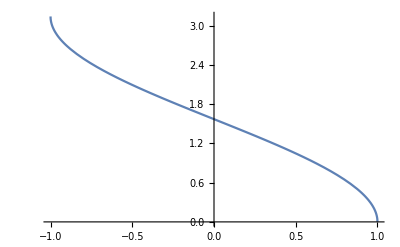

```mathematica
Plot[ArcCos[x],{x,-1,1}]
```

```mathematica
RX[{3.54353,2.234234,6}]
```

{35.435,22.342,60}